## Solutions S_01and S_02

```mathematica
ClearAll["Global`*"]
```

```mathematica
bar[I0_,Ak_]:=I0*Ak;
(* The Intrinsic Spin terms *)
Subscript[P, 31][Spin_,j_,I0_,A1_,A3_]:=(2Spin-1)(bar[I0,A3]-bar[I0,A1])+2*j*bar[I0,A1];
Subscript[P, 21][Spin_,j_,I0_,A1_,A2_]:=(2Spin-1)(bar[I0,A2]-bar[I0,A1])+2*j*bar[I0,A1];
(* The Single-particle terms *)
Subscript[Q, 31][Spin_,j_,I0_,A1_,A3_]:=(2j-1)(bar[I0,A3]-bar[I0,A1])+2Spin*bar[I0,A1];
Subscript[Q, 21][Spin_,j_,I0_,A1_,A2_]:=(2j-1)(bar[I0,A2]-bar[I0,A1])+2Spin*bar[I0,A1];
(* The triaxial terms *)
Subscript[G, 1][j_,γ_]:=(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]);
Subscript[G, 2][j_,γ_]:=(2j-1)/(j(j+1))2 √3 Sin[γ*π/180];
```

### Define S_01 and S_02

```mathematica
Subscript[S, 01][I0_,Spin_,j_,γ_,A1_,A2_,A3_]:=(4*Spin*j*bar[I0,A3]^2-Subscript[P, 31][Spin,j,I0,A1,A3]*Subscript[Q, 31][Spin,j,I0,A1,A3])/(Subscript[P, 31][Spin,j,I0,A1,A3]*Subscript[G, 1][j,γ]);
Subscript[S, 02][I0_,Spin_,j_,γ_,A1_,A2_,A3_]:=(4*Spin*j*bar[I0,A2]^2-Subscript[P, 21][Spin,j,I0,A1,A3]*Subscript[Q, 21][Spin,j,I0,A1,A3])/(Subscript[P, 21][Spin,j,I0,A1,A3]*Subscript[G, 2][j,γ]);
```

#### Numerical parameters

```mathematica
ak={0.01,0.3,0.9};
```

```mathematica
cpS01=ContourPlot[{Subscript[S, 01][x*y,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]]},{x,0,60},{y,0,5},Contours->30,ContourShading->None,ContourStyle->Directive[Blue]];
cpS02=ContourPlot[{Subscript[S, 02][x*y,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]]},{x,0,60},{y,0,5},Contours->30,ContourShading->None,ContourStyle->Directive[Thick,Dashed,Red]];
```

```mathematica
Subscript[F, 1][I0_,V_,Spin_,j_,γ_,A1_,A2_,A3_]:=Subscript[P, 31][Spin,j,I0,A1,A3]*Subscript[G, 1][j,γ]*(I0*V)+Subscript[P, 31][Spin,j,I0,A1,A3]*Subscript[Q, 31][Spin,j,I0,A1,A3]-4Spin*j*bar[I0,A3]^2;
Subscript[F, 2][I0_,V_,Spin_,j_,γ_,A1_,A2_,A3_]:=Subscript[P, 21][Spin,j,I0,A1,A2]*Subscript[G, 2][j,γ]*(I0*V)+Subscript[P, 21][Spin,j,I0,A1,A2]*Subscript[Q, 21][Spin,j,I0,A1,A2]-4Spin*j*bar[I0,A2]^2;
```

```mathematica
Solve[Subscript[F, 1][I0,x,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]]==0,x]
Solve[Subscript[F, 2][I0,x,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]]==0,x]
```

{{x→1.29182}}

{{x→0.746735}}

```mathematica
Subscript[F, 1][10,1.2918185739646788,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]]
```

7.27596×10^-12

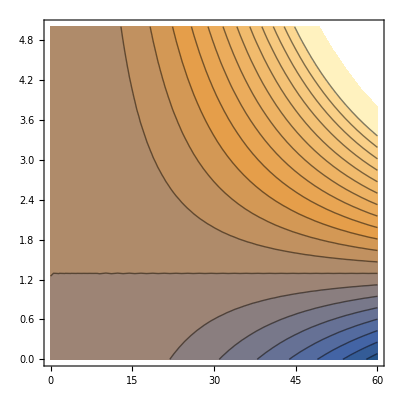

```mathematica
ContourPlot[Subscript[F, 1][x,y,35/2,13/2,25,ak[[1]],ak[[2]],ak[[3]]],{x,0,60},{y,0,5},Contours->20]
```